## Constants + Cases

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.511*10^6; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Cases*)
CBETA150={Ee->150*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.435*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.126976,σL->25*10^-6,ΔEe->5*10^-4,L->10};
```

```mathematica
trialcase=CBETA150;
```

## Preliminaries

```mathematica
θob[θx_,yc_,L_]:=Sqrt[θx^2+(yc/L)^2];
```

```mathematica
(*Intermediary calculations for the scattered photon energy*)
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
(*Preliminaries*)
σe[ΔEe_,Ee_]:=ΔEe*Ee; (*Conversion from relative*)
```

```mathematica
(*Collimation*)
R[L_,θcol_]:=L*θcol;
x0[L_,θcol_]:=R[L,θcol]; (*Condition for circular collimator*) 
y0[L_,θcol_]:=R[L,θcol];
```

```mathematica
(*Term 3 calculations*)
ϵx[Ee_,ϵnx_]:=ϵnx/γ[Ee];
k[λ_]:=EL[λ]/(hbar*clight);
zr[λ_,σL_]:=(π*σL^2)/λ;
a[λ_]:=EL[λ]/me;
ξx[βx_,L_,λ_,Ee_,ϵnx_,σL_]:=1+(βx/L)^2+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζx[λ_,βx_,Ee_,ϵnx_,σL_]:=1+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,λ,Ee,ϵnx,σL])/(βx*ζx[λ,βx,Ee,ϵnx,σL])];
γbar[λ_,Eγ_,θx_,yc_,L_]:=(2*Eγ*a[λ])/(4*EL[λ]-Eγ*θob[θx,yc,L]^2)*(1+Sqrt[1+(4*EL[λ]-Eγ*θob[θx,yc,L]^2)/(4*a[λ]^2*Eγ)]);
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θxmax[λ_,Eγ_,yc_,L_]:=Sqrt[(4*EL[λ])/Eγ-(yc/L)^2];
```

## Inspection of Term 3

```mathematica
term3[θx_,xc_,L_,Ee_,ϵnx_,βx_,λ_,σL_,yc_,ΔEe_,Eγ_]:=Exp[(-(θx-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)-(γbar[λ,Eγ,θx,yc,L]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)];
```

```mathematica
INTterm3[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
Term3dat=Table[{Eγ,INTterm3[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

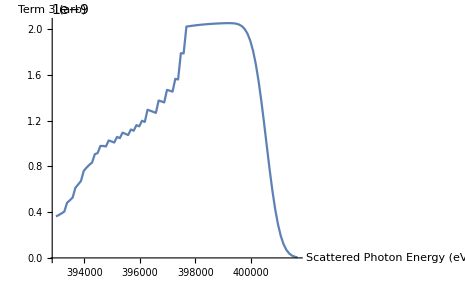

```mathematica
ListLinePlot[Term3dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 3 (arb)"}]
```

## θxmax Limit

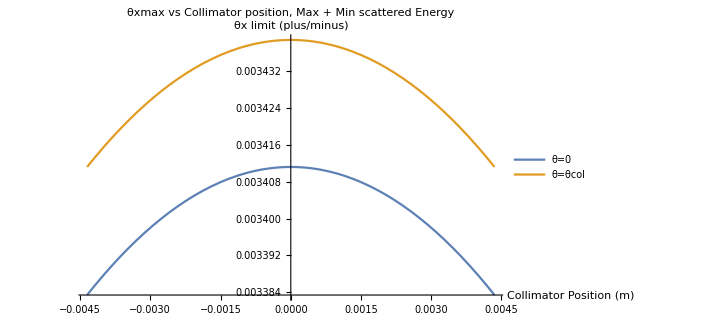

```mathematica
Plot[{θxmax[λ,Eγset[λ,Ee,ϕ,0],yc,L]/.trialcase,θxmax[λ,Eγset[λ,Ee,ϕ,θcol],yc,L]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},AxesLabel->{"Collimator Position (m)","θx limit (plus/minus)"},PlotLabel->"θxmax vs Collimator position, Max + Min scattered Energy",PlotLegends->Placed[{"θ=0","θ=θcol"},{0.7,0.3}]]
```

```mathematica
PreExp3a[λ_,Eγ_,yc_,L_,xc_,Ee_,ϵnx_,βx_,σL_]:=(-(θxmax[λ,Eγ,yc,L]-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2);
```

```mathematica
Plot3D[{PreExp3a[λ,Eγset[λ,Ee,ϕ,0],yc,L,xc,Ee,ϵnx,βx,σL]/.trialcase,PreExp3a[λ,Eγset[λ,Ee,ϕ,θcol],yc,L,xc,Ee,ϵnx,βx,σL]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase}]
```

-Graphics3D-

```mathematica
Exp3a[λ_,Eγ_,yc_,L_,xc_,Ee_,ϵnx_,βx_,σL_]:=Exp[(-(θxmax[λ,Eγ,yc,L]-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)];
```

```mathematica
Plot3D[{Exp3a[λ,Eγset[λ,Ee,ϕ,0],yc,L,xc,Ee,ϵnx,βx,σL]/.trialcase,Exp3a[λ,Eγset[λ,Ee,ϕ,θcol],yc,L,xc,Ee,ϵnx,βx,σL]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase}]
```

-Graphics3D-

## Inspection of Spatial Term

```mathematica
term3a[θx_,xc_,L_,Ee_,ϵnx_,βx_,λ_,σL_]:=Exp[(-(θx-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)];
```

```mathematica
(*Try to plot out this function at the peak energy, difficult as θx limits use yc which is not included in the plotting - picked yc=R*)
tab3a=Table[term3a[θx,xc,L,Ee,ϵnx,βx,λ,σL]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase,100},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase,100},{θx,-θxmax[λ,Eγset[λ,Ee,ϕ,0]/.trialcase,yc,L]/.trialcase,θxmax[λ,Eγset[λ,Ee,ϕ,0]/.trialcase,yc,L]/.trialcase,100}]
```

{{{3.11412×10^-235}}}

```mathematica
ListPlot[tab3a]
```

-Graphics-

```mathematica
INTterm3a[L_,Ee_,ϵnx_,βx_,λ_,σL_,Eγ_]:=NIntegrate[term3a[L,Ee,ϵnx,βx,λ,σL]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
INTterm3a[L,Ee,ϵnx,βx,λ,σL,Eγset[λ,Ee,ϕ,0]/.trialcase]
```

NIntegrate::inumr: The integrand term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate[term3a[L,Ee,ϵnx,βx,λ,σL]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,400553.,yc,L]/.trialcase,θxmax[λ,400553.,yc,L]/.trialcase}]

```mathematica
Term3adat=Table[{Eγ,INTterm3a[L,Ee,ϵnx,βx,λ,σL,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,100}];
```

NIntegrate::inumr: The integrand term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
ListLinePlot[Term3adat,AxesLabel->{"Scattered Photon Energy (eV)","Term 3a (arb)"}]
```

NIntegrate::inumr: The integrand term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

## Inspection of Energy Exponential Term

```mathematica
term3b[λ_,Eγ_,θx_,yc_,L_,Ee_,ΔEe_]:=Exp[(-(γbar[λ,Eγ,θx,yc,L]-γ[Ee])^2)/(2*σγ[ΔEe,Ee]^2)];
```

```mathematica
INTterm3b[λ_,Eγ_,L_,Ee_,ΔEe_]:=NIntegrate[term3b[λ,Eγ,θx,yc,L,Ee,ΔEe]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
Term3bdat=Table[{Eγ,INTterm3b[λ,Eγ,L,Ee,ΔEe]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

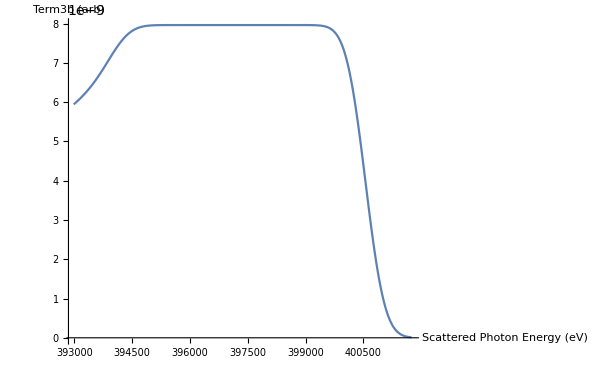

```mathematica
ListLinePlot[Term3bdat,AxesLabel->{"Scattered Photon Energy (eV)","Term3b (arb)"}]
```

## Inspection of Terms Together

```mathematica
(*Should just replicate term3*)
INTterm3alt[L_,Ee_,ϵnx_,βx_,λ_,σL_,Eγ_,ΔEe_]:=NIntegrate[(term3a[L,Ee,ϵnx,βx,λ,σL]/.trialcase)*(term3b[λ,Eγ,θx,yc,L,Ee,ΔEe]/.trialcase),{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
Term3altdat=Table[{Eγ,INTterm3alt[L,Ee,ϵnx,βx,λ,σL,Eγ,ΔEe]},{Eγ,Eγset[λ,Ee*(1-5*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,100}];
```

NIntegrate::inumr: The integrand ⅇ^(-23.2108 (-293.542+(1.78875 (1+Power[«2»]))/Plus[«2»])^2) term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-23.2108 (-293.542+(1.78921 (1+Power[«2»]))/Plus[«2»])^2) term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-23.2108 (-293.542+(1.78967 (1+Power[«2»]))/Plus[«2»])^2) term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Term3altdat
```

NIntegrate::inumr: The integrand ⅇ^(-23.2108 (-293.542+(1.78875 (1+Power[«2»]))/Plus[«2»])^2) term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-23.2108 (-293.542+(1.78921 (1+Power[«2»]))/Plus[«2»])^2) term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-23.2108 (-293.542+(1.78967 (1+Power[«2»]))/Plus[«2»])^2) term3a[10,150000000,3.×10^-7,0.126976,133/125000000,1/40000] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{392210.,NIntegrate[(term3a[L,Ee,ϵnx,βx,λ,σL]/.trialcase) (term3b[λ,392210.,θx,yc,L,Ee,ΔEe]/.trialcase),{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,392210.,yc,L]/.trialcase,θxmax[λ,392210.,yc,L]/.trialcase}]},94,{401710.,NIntegrate[(term3a[L,Ee,ϵnx,βx,λ,σL]/.trialcase) (term3b[λ,401710.,θx,yc,L,Ee,ΔEe]/.trialcase),{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,401710.,yc,L]/.trialcase,θxmax[λ,401710.,yc,L]/.trialcase}]}}
 |  |  |  |